```mathematica
(*
	Questa funzione disegna un grafo di Levi.

   INPUT:   cx     Coordinata X del centro del grafo (default 0)
		  tipo   Tipo grafo (0=Don't care,1=Fano,2=Tutte-Coxeter) (default 1)
		  prm    Permutazione degli n nodi (default la permutazione identica)
		  nfs    Rotazione del grafo. Viene realizzata una rotazione in senso antiorario di angolo nsf*(360/n gradi)
		         Se nfs e' intero questo corrisponde ad una rotazione dei nodi. (default 0)
		  nn     Numero di nodi del grafo (numero pari) (default 4)
          lagg   Lista connessioni interne di n nodi (default {1,2,3,4})
		  sgl    Sigle nodi elementi (default {1,2,3,4})
	      
	      
OUTPUT:  Lista elementi da graficare
     
*)
genLevi[cx_:0,tipo_:1,prm_:{0},nfs_:0,nn_:4,lagg_:{1,2,3,4},sgl_:{1,2,3,4}]:=(
If[tipo==0,n=nn;lpagg=lagg;
If[sgl[[1]]==0,sigle=Range[n],sigle=sgl]];
If[tipo==1,n=14;
lpagg={10,7,12,9,14,11,2,13,4,1,6,3,8,5};
sigle={1,2,3,4,5,6,7,8,9,10,11,12,13,14}];
If[tipo==2,n=30;lpagg={14,19,24,11,28,15,20,25,30,17,4,21,26,1,6,23,10,27,2,7,12,29,16,3,8,13,18,5,22,9};sigle={12,13,14,15,16,23,24,25,26,34,35,36,45,46,56}];

If[prm[[1]]==0,perm=Range[n],perm=prm];

clr1=Black;
clr2=Green;
cy=0;
r=10;
dfs=Pi/2+Pi/n;
da=2Pi/n;

lcoo=Range[n];
lcoot1=Range[n];
lcoot2=Range[n];
lcoot3=Range[n];
ang=0;
offs1=2;
offs2=4;
offs3=6;
fs=nfs 2Pi/n ;
For[k=1,k≤n,k++,
pp={cx+r Cos[ang+dfs+fs],cy+r Sin[ang+dfs+fs]};
lcoo[[perm[[k]]]]=pp;
lcoot1[[perm[[k]]]]={pp[[1]]+offs1 Cos[ang+dfs+fs],pp[[2]]+offs1 Sin[ang+dfs+fs] };
lcoot2[[perm[[k]]]]={pp[[1]]+offs2 Cos[ang+dfs+fs],pp[[2]]+offs2 Sin[ang+dfs+fs] };
lcoot3[[perm[[k]]]]={pp[[1]]+offs3 Cos[ang+dfs+fs],pp[[2]]+offs3 Sin[ang+dfs+fs] };
ang-=da;
];

colors={"Red","Blue"};
p=Range[n];
sizep=10;

For[k=1,k≤n,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[sigle[[Floor[k/2]+1]],lcoot1[[k]]]};
];
For[k=2,k≤n,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[sigle[[Mod[Floor[(k-2)/2],n/2]+1]],lcoot1[[k]]],Text[sigle[[Mod[Floor[k/2],n/2]+1]],lcoot2[[k]]]};If[lpagg[[1]]≠ 0,AppendTo[p[[k]],{Text[sigle[[Floor[lpagg[[k]]/2+1]]],lcoot3[[k]]]}]];
];

ln=Range[n];
For[k=1,k<n,k++,
ln[[k]]=Line[{lcoo[[k]],lcoo[[k+1]]}];
];
ln[[n]]=Line[{lcoo[[n]],lcoo[[1]]}];

If[lpagg[[1]]==0,Return[{p,{clr1,ln}}],
lnaus=Range[n];
For[k=1,k≤n,k++,
lnaus[[k]]=Line[{lcoo[[k]],lcoo[[lpagg[[k]]]]}]]
];

Return[{p,{clr1,ln},{clr2,lnaus}}];
)

(*
	Questa funzione applica una serie di trasposizioni ad una permutazione di partenza

	INPUT: per insieme delle trasposizioni da applicare
		 n   numero di elementi della permutazione di partenza
		 prm permutazione di partenza (default la permutazione identica su n elementi)
*)
genPerm[per_,n_,prm_:{0}]:=(
If[prm[[1]]==0,result=Range[n],result=prm];
nel1=Length[per];
For[k1=1,k1≤nel1,k1++,
nel2=Length[per[[k1]]];
For[k2=nel2,k2>=1,k2--,
inda=per[[k1]][[k2]];
If[k2<nel2,result[[indp]]=result[[inda]],appo=result[[inda]]];
indp=inda;
];
result[[indp]]=appo;
];
Return[result];
)

(*
	Questa funzione applica una riflessione ad una permutazione iniziale di vertici
   La riflessione e' effettuata rispetto ad un asse che passa per il vertice v1
   se v1=v2 o passa per la mediana del lato che congiunge v1 a v2 (dovra' essere v2=(v1+1 modulo n) 

	INPUT: v1  primo vertice
		 v2  secondo vertice
		 n   numero dei vertici
		 prm permutazione iniziale di n vertici
*)
genRiflex[v1_,v2_,n_,prm_:{0}]:=(
If[prm[[1]]==0,result=Range[n],result=prm];
If[v1==v2,
v=v1;
For[k=1,k≤Floor[(n-1)/2],k++,
appo=result[[Mod[v-1-k,n]+1]];
result[[Mod[v-1-k,n]+1]]=result[[Mod[v-1+k,n]+1]];
result[[Mod[v-1+k,n]+1]]=appo
],
For[k=1,k≤Floor[n/2],k++,
appo=result[[Mod[v1-k,n]+1]];
result[[Mod[v1-k,n]+1]]=result[[Mod[v2+k-2,n]+1]];
result[[Mod[v2+k-2,n]+1]]=appo
]
];
Return[result];
)
```

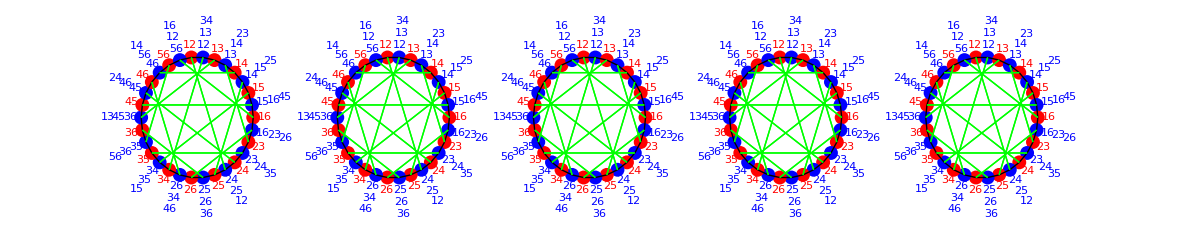

```mathematica
gen1={{5,11},{6, 10},{7, 17},{8 ,16},{9, 15},{12, 28},{13, 29},{14, 30},{18, 20},{21, 27},{22, 26},{23 ,25}};
gen2={{5,11},{6, 12},{7, 21},{8 ,22},{9, 29},{10, 28},{13, 15},{16, 26},{17, 27},{23, 25}};
gen3={{2,14},{3, 15},{4, 6},{7 ,11},{8, 10},{12, 20},{13, 19},{16, 24},{17, 25},{18, 26}};
gen4={{1,2,3, 4,5, 6,7 ,8,9, 30},{10, 29,14, 19,24, 11,28, 15,20, 25},{12, 27,16 ,21,26,17,22,13,18,23}};

g1=genLevi[0,2];
g2=genLevi[35,2,gen1];
g3=genLevi[70,2,gen2];
g4=genLevi[105,2,gen3];
g5=genLevi[140,2,gen4];
Graphics[{g1,g2,g3,g4,g5}]
```

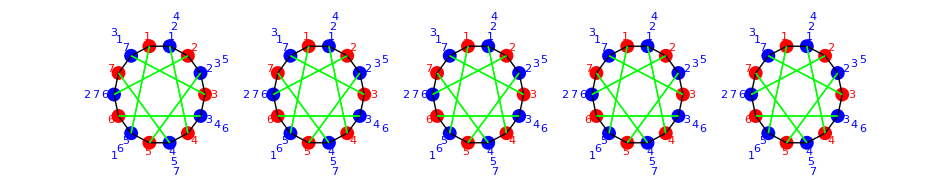

```mathematica
gen1={{5,9},{6,8},{10,14},{11,13}};
gen2={{4,12},{5,11},{9,13},{10,14}};
gen3={{2,14},{3,5},{6,12},{7,13}};
gen4={{1,3},{4,14},{9,13},{10,12}};

g1=genLevi[0];
g2=genLevi[35,1,gen1];
g3=genLevi[70,1,gen2];
g4=genLevi[105,1,gen3];
g5=genLevi[140,1,gen4];
Graphics[{g1,g2,g3,g4,g5}]
```

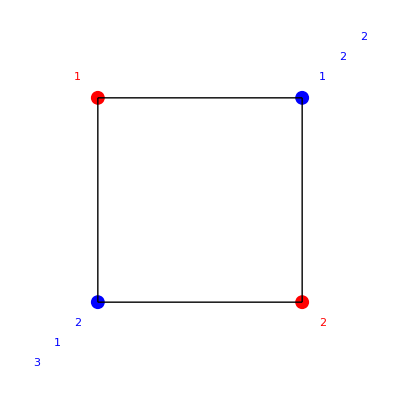

```mathematica
Graphics[genLevi[0,0,{0}]]
```

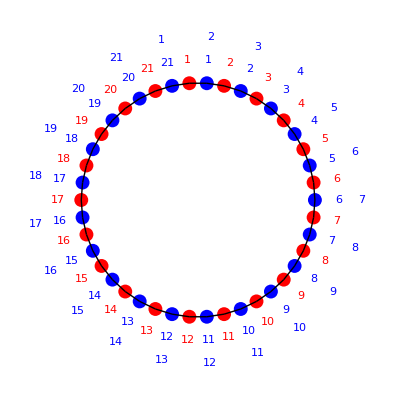

```mathematica
g1=genLevi[0,0,{0},0,42,{0},{0}];
Graphics[g1]
```